```mathematica
a[e_]:=6.67*10^-11 * 5.97 * 10^24 / (e+6370000)^2
```

```mathematica
(a[8848]-9.8)/a[8848]
```

-0.00140653

```mathematica
(9.793922-9.83366)/9.81
```

-0.00405076

```mathematica
data=Import["http://www.cs.utexas.edu/~evanott/PHY110C_Textbook/static/data_analysis/_downloads/assignment3data.csv"];
```

```mathematica
halley=data[[All,31;;33]];
```

```mathematica
ListPointPlot3D[halley-sun]
```

-Graphics3D-

```mathematica
sun = data[[All,1;;3]];
```

```mathematica
halley[[1]]
```

{8.8353×10^10,0.,0.}

```mathematica
halley2d=(halley-sun)[[All,1;;2]]
```

{{8.8353×10^10,0.},{8.83529×10^10,1.33812×10^8},{8.83528×10^10,2.67623×10^8},«14918»,{-5.76079×10^11,4.49136×10^11},{-5.76112×10^11,4.49146×10^11},{-5.76146×10^11,4.49155×10^11}}

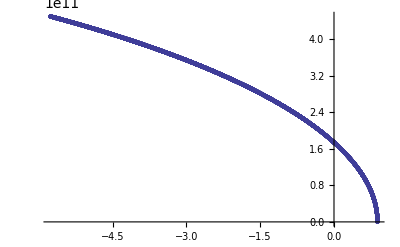

```mathematica
ListPlot[halley2d]
```

```mathematica
thetaList=Mod[ArcTan[halley2d[[All,2]]/halley2d[[All,1]]]+2Pi,Pi];
rList=Sqrt[halley2d[[All,1]]^2+halley2d[[All,2]]^2];
thetaRList=Table[{thetaList[[i]],rList[[i]]},{i,1,Length[halley2d]}]
```

{{0.,8.8353×10^10},{0.00151451,8.8353×10^10},{0.00302902,8.83532×10^10},«14918»,{2.47939,7.30473×10^11},{2.47941,7.30505×10^11},{2.47942,7.30537×10^11}}

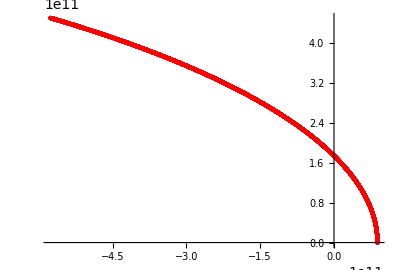

```mathematica
Show[ListPolarPlot[thetaRList,PlotStyle->PointSize[Large]],ListPlot[halley2d,PlotStyle->Directive[Red,PointSize[Small]]]]
```

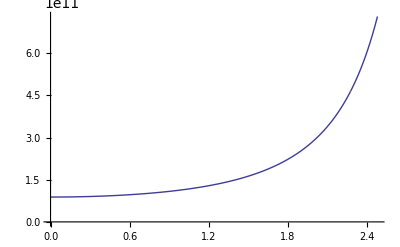

```mathematica
ListPlot[%685,Joined->True]
```

```mathematica
Module[{c,e},FindFit[thetaRList,c/(1+e Cos[theta]),{c,e},{theta}]]
```

{c$149004→1.73727×10^11,e$149004→0.966439}

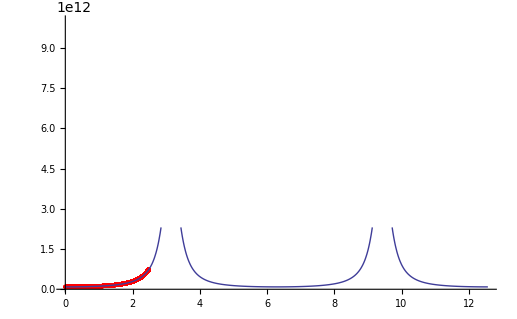

```mathematica
Show[ListPlot[thetaRList,PlotStyle->Red],Plot[c/(1+e Cos[theta])/.{c->1.7372705457425507*^11,e->0.9664392262159686},{theta,0,4Pi}],PlotRange->{{0,4Pi},{10^11,10^13}}]
```

```mathematica
fitted[theta_]:=c/(1+e Cos[theta])/.{c->1.7372705457425507*^11,e->0.9664392262159686}
```

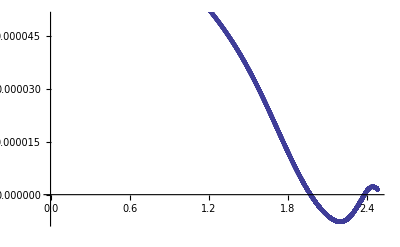

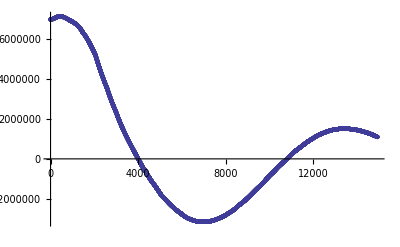

```mathematica
resid = Table[{thetaRList[[i,1]],(thetaRList[[i,2]]-fitted[thetaRList[[i,1]]])/thetaRList[[i,2]]},{i,1,Length[thetaRList]}];
ListPlot[resid]
```

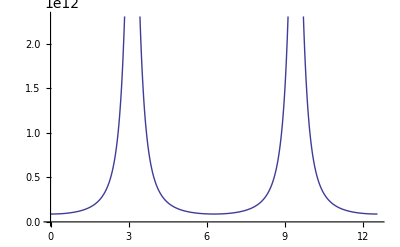

```mathematica
Plot[c/(1+e Cos[theta])/.{c->1.7372705457425507*^11,e->0.9664392262159686},{theta,0,4Pi}]
```

```mathematica
μ=2.2*10^14 * 1.989*10^30/(1.989*10^30+2.2*10^14)
```

2.2×10^14

```mathematica
γ=6.67*10^-11*2.2*10^14 * 1.989*10^30
```

2.91866×10^34

```mathematica
l=Sqrt[γ μ c]
```

1.05618×10^30

```mathematica
e=0.9664392262159686
```

0.966439

```mathematica
c=1.7372705457425507*^11
```

1.73727×10^11

```mathematica
a=c/(1-e^2)
```

2.63242×10^12

```mathematica
2 Pi Sqrt[a^3/(6.67*10^-11 * 1.989*10^30)]/(3600 * 24 * 365.25)
```

73.8292